### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

```mathematica
?SSS
```

```mathematica
?SSSInitialState
```

```mathematica
?FromReducedRankIndex
```

```mathematica
FromReducedRankIndex[5898765100]
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

```mathematica
SSSInitialState[{"AA"->"B","AB"->"BA","BC"->"AAA"}]
```

AABABCB

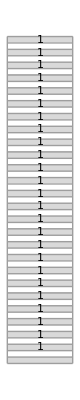
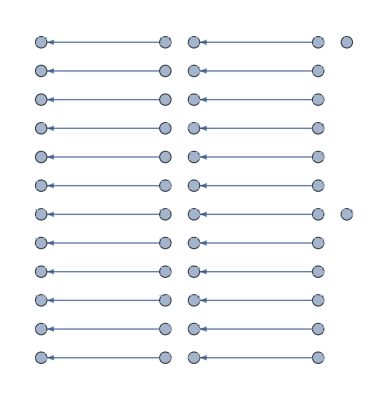
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Net→{2→3,4→5,6→7,8→9,10→11,12→13,14→15,16→17,18→19,20→21,22→23,24→25,26→27,28→29,30→31,32→33,34→35,36→37,38→39,40→41,42→43,44→45,46→47,48→49},OutDegreePotential→{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},OutDegreeRemaining→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},OutDegreeActual→{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0},InDegree→{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},ConnectionList→{{1}→{},{}→{2},{2}→{},{}→{3},{3}→{},{}→{4},{4}→{},{}→{5},{5}→{},{}→{6},{6}→{},{}→{7},{7}→{},{}→{8},{8}→{},{}→{9},{9}→{},{}→{10},{10}→{},{}→{11},{11}→{},{}→{12},{12}→{},{}→{13},{13}→{},{}→{14},{14}→{},{}→{15},{15}→{},{}→{16},{16}→{},{}→{17},{17}→{},{}→{18},{18}→{},{}→{19},{19}→{},{}→{20},{20}→{},{}→{21},{21}→{},{}→{22},{22}→{},{}→{23},{23}→{},{}→{24},{24}→{},{}→{25},{25}→{},{}→{26}},Verdict→Repeating,RulesUsed→{1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},CellsDeleted→{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{}},Distance→{0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},MaxColor→6,TagIndex→27,TEvolution→{s[{0,1}],s[],s[{0,2}],s[],s[{0,3}],s[],s[{0,4}],s[],s[{0,5}],s[],s[{0,6}],s[],s[{0,7}],s[],s[{0,8}],s[],s[{0,9}],s[],s[{0,10}],s[],s[{0,11}],s[],s[{0,12}],s[],s[{0,13}],s[],s[{0,14}],s[],s[{0,15}],s[],s[{0,16}],s[],s[{0,17}],s[],s[{0,18}],s[],s[{0,19}],s[],s[{0,20}],s[],s[{0,21}],s[],s[{0,22}],s[],s[{0,23}],s[],s[{0,24}],s[],s[{0,25}],s[],s[{0,26}]},Evolution→{A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A},RuleSet→{A→,→A},TRuleSet→{s[{0,lhsTag$22730_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$22730}→$SSSTagIndex+{}];s[]),s[]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{}→$SSSTagIndex+{0}];s[{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]},RuleSetWeight→2,RuleSetLength→2|>

```mathematica
SSS[2,50];
```

```mathematica
IndexedConcatenate
```

```mathematica
?IndexedConcatenation
```

### Examples of simple (and then more and more complex) IC objects:

```mathematica
{IndexedConcatenate[A, B, C, {n,1,5}]}
```

{€_(n⊨1)^5[A,B,C]}

```mathematica
{IndexedConcatenate[A, B, C, {n,1,5}]}//ExpandAll
```

{A,B,C,A,B,C,A,B,C,A,B,C,A,B,C}

```mathematica
{A,B,C} ⧺ {A,B,C} ⧺ {A,B,C} ⧺ {A,B,C} ⧺ {A,B,C}
```

```mathematica
{A,B,C} ~Concatenate~ {A,B,C} ~Concatenate~ {A,B,C} ~Concatenate~ {A,B,C} ~Concatenate~ {A,B,C}
```

{A,B,C,A,B,C,A,B,C,A,B,C,A,B,C}

```mathematica
A ~Concatenate~ B ~Concatenate~ C
```

A⧺B⧺C

```mathematica
{IndexedConcatenate[S, 3]}
```

{€^3[S]}

```mathematica
{IndexedConcatenate[S, 3]}//ExpandAll
```

{S,S,S}

```mathematica
{IndexedConcatenate[S, {n,1,3}]}//ExpandAll
```

{S,S,S}

```mathematica
{IndexedConcatenate[1, 3]}
```

{€^3[1]}

```mathematica
{IndexedConcatenate[1, 3]}//ExpandAll
```

{1,1,1}

```mathematica
{IndexedConcatenate[1,2,3, 3]}
```

{€^3[1,2,3]}

```mathematica
{IndexedConcatenate[1,2,3, 3]}//ExpandAll
```

{1,2,3,1,2,3,1,2,3}

```mathematica
{IndexedConcatenate[i,2i,3i, {i,1,4}]}
```

{€_(i⊨1)^4[i,2 i,3 i]}

```mathematica
{IndexedConcatenate[i,2i,3i, {i,1,4}]}//ExpandAll
```

{1,2,3,2,4,6,3,6,9,4,8,12}

```mathematica
{IndexedConcatenate[{i,2i,3i}, {i,1,4}]}
```

{€_(i⊨1)^4[{i,2 i,3 i}]}

```mathematica
{IndexedConcatenate[{i,2i,3i}, {i,1,4}]}//ExpandAll
```

{{1,2,3},{2,4,6},{3,6,9},{4,8,12}}

```mathematica
{IndexedConcatenate[IndexedConcatenate[FractionBox[n,d-n+1],{n,1,d}], {d,1,5}]}
```

{€_(d⊨1)^5[€_(n⊨1)^d[n/(d-n+1)]]}

Cantor’s enumeration of the Rationals:

```mathematica
{IndexedConcatenate[IndexedConcatenate[FractionBox[n,d-n+1],{n,1,d}], {d,1,5}]}//ExpandAll//DisplayForm
```

{1/1,1/2,2/1,1/3,2/2,3/1,1/4,2/3,3/2,4/1,1/5,2/4,3/3,4/2,5/1}

```mathematica
{IndexedConcatenate[{IndexedConcatenate[FractionBox[n,d-n+1],{n,1,d}]}, {d,1,5}]}
```

{€_(d⊨1)^5[{€_(n⊨1)^d[n/(d-n+1)]}]}

```mathematica
{IndexedConcatenate[{IndexedConcatenate[FractionBox[n,d-n+1],{n,1,d}]}, {d,1,5}]}//ExpandAll//DisplayForm
```

{{1/1},{1/2,2/1},{1/3,2/2,3/1},{1/4,2/3,3/2,4/1},{1/5,2/4,3/3,4/2,5/1}}

```mathematica
IndexedConcatenate[{1,k^j},{j,0,5}]
```

```mathematica
€_(j⊨0)^5[{1,k^j}]
```

```mathematica
{IndexedConcatenate[{1,2^j},{j,0,5}]}//ExpandAll
```

{{1,1},{1,2},{1,4},{1,8},{1,16},{1,32}}

```mathematica
ReduceSetList[%87]
```

{€_(n$1⊨1)^6[{1,2^(-1+n$1)}]}

```mathematica
{IndexedConcatenate[1,2^j,{j,0,5}]}//ExpandAll
```

{1,1,1,2,1,4,1,8,1,16,1,32}

```mathematica
ReduceSetList@%
```

{€^3[1],€_(n$1⊨1)^4[2^n$1,1],32}

```mathematica
{IndexedConcatenate[(1-(-1)^j)/2+(1+(-1)^j)/2 2^j,{j,0,10}]}//ExpandAll
```

{1,1,4,1,16,1,64,1,256,1,1024}

```mathematica
Table[{j,(1-(-1)^j)/2 2^j,(1+(-1)^j)/2},{j,0,5}]//Grid
```

0 | 0 | 1
1 | 1 | 0
2 | 0 | 1
3 | 1 | 0
4 | 0 | 1
5 | 1 | 0